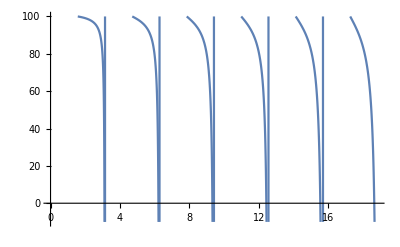

{k→3.13845}

{k→6.27691}

{k→9.41536}

{k→12.5538}

{k→15.6923}

{k→18.8307}

{k→21.9692}

{k→25.1076}

{k→28.2461}

```mathematica
Clear[KL]
Plot[KL+ k Cot[k]/. KL -> 100., {k,0,6π}, PlotRange -> {-10, 100}]
For[n=1,n<10,n++,Print[FindRoot[KL+k Cot[k]/. KL -> 1000., {k, n*π*.9999}]]]
```